## Тест 1

#### Тысячные

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Pois_eq.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Pois_eq.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение тест 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
```

```mathematica
Plot3D[1+x2,{x1,0,L},{x2,0,L},PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение тест 3

```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
```

```mathematica
Plot3D[x1^2+x2^2,{x1,0,L},{x2,0,L},PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Проверка порядков

```mathematica
ClearAll["`*"];
```

```mathematica
ω=1;tk=1.0;
 DSolve[{D[u[x,t],t]==1/ω D[u[x,t],{x,2}],u[x,0]==2Sin[ω x],u[0,t]==0,u[π/(2ω),t]==2Exp[-ω t]},u[x,t],x,t]⟦1⟧⟦1⟧⟦2⟧;
```

```mathematica
Sol[x_,t_]=%;
```

```mathematica
NotebookDirectory[];
n = 2;
For[i=1,i≤5,i++,len=0;
Subscript[plots, i]=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integro_interpolation_mult_1.000000_"<>ToString[2^i]<>".000000.txt"]],Table[Real,n+1]];
Subscript[Diff, i]= Table[Abs[Sol[Subscript[plots, i]⟦k⟧⟦2⟧,Subscript[plots, i]⟦k⟧⟦1⟧]-Subscript[plots, i]⟦k⟧⟦3⟧],{k,1,Length[Subscript[plots, i]]}];Subscript[Err, i] = Max[Subscript[Diff, i]];]
```

```mathematica
GridData=Join[{{"τ, h","AbsErr(τ, h)","Δ", "log_qΔ"}},Table[{{0.1 * (1/2)^(j-1),0.1*1/2^(j-1)},Subscript[Err, j],Subscript[Err, j]/Subscript[Err, j-1],-Log[Subscript[Err, j]/Subscript[Err, j-1]]/Log[2]},{j,1,5}]];
```

```mathematica
GridData⟦2⟧⟦3⟧=0;
GridData⟦2⟧⟦4⟧=0;
```

```mathematica
Grid[GridData,Frame->All]
```

τ, h | AbsErr(τ, h) | Δ | log_qΔ
{0.1,0.1} | 0.00654447 | 0 | 0
{0.05,0.05} | 0.00281905 | 0.430754 | 1.21506
{0.025,0.025} | 0.000860095 | 0.305101 | 1.71264
{0.0125,0.0125} | 0.000209965 | 0.244119 | 2.03435
{0.00625,0.00625} | 0.0000525069 | 0.250074 | 1.99957

## Количество итераций

```mathematica
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Non_linear_iter.txt"]],Table[Real,n+1]];
```

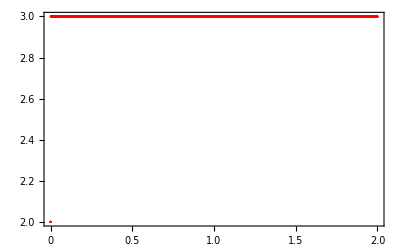

```mathematica
ListPlot[plots,PlotStyle->Red,PlotTheme->"Web"]
```